```mathematica
(* MA39110 / Assignment 2.4 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=1;h=(xf-x0)/n;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X =Table[x0+x*h,{x,1,n-1}];
B =Table[0,{x,1,n-1}];
For[i=1,i<n,i++,
{
A[[i,i]]=1-2/h^2;
If[i≠1,A[[i,i-1]]=1/h^2];
If[i≠n-1,A[[i,i+1]]=1/h^2,B[[i]]=-1/h^2];
}];
Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B]];
```

```mathematica
sol=Model[4];
solt=DSolve[{y''[x]+y[x]==0,y[0]==0,y[1]==1},y[x],x]
err1=Abs[DSolveValue[{y''[x]+y[x]==0,y[0]==0,y[1]==1},y[X],x]-sol];
perr1 = ListPlot[Transpose[{X,err1}],PlotStyle->Red];
N[Max[err1]]
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.25",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

{{y[x]→Csc[1] Sin[x]}}

0.000408938

```mathematica
sol=Model[8];
err2=Abs[DSolveValue[{y''[x]+y[x]==0,y[0]==0,y[1]==1},y[X],x]-sol];
perr2 = ListPlot[Transpose[{X,err2}],PlotStyle->Green];
N[Max[err2]]
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.25/2",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

0.000101708

```mathematica
sol=Model[16];
err3=Abs[DSolveValue[{y''[x]+y[x]==0,y[0]==0,y[1]==1},y[X],x]-sol];
perr3=ListPlot[Transpose[{X,err3}],PlotStyle->Blue];
N[Max[err3]]
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.25/4",FontSize->18]]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

0.0000258177

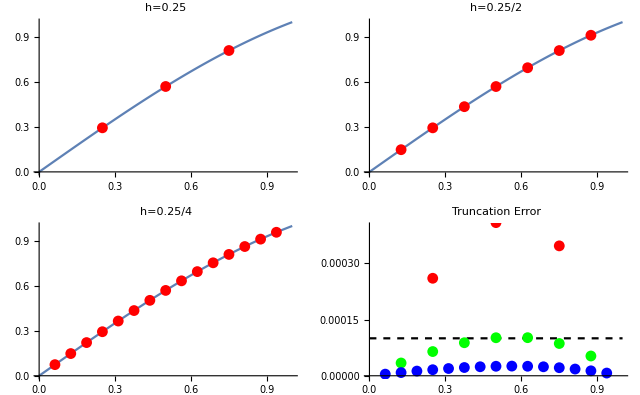

```mathematica
p4=Show[{Plot[y[x]=10^-4,{x,0,1},PlotStyle->{Dashed,Black}]},{perr1},{perr2},{perr3},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,1},{0,0.0004}}];
GraphicsGrid[{{p1,p2},{p3,p4}}]
```